# Lab E1: Introduction to Circuits

## Introduction:

The main purpose and goal for this lab was to introduce us students to circuits. This lab introduces the digital multimeter(measuring current, resistance and voltage), DC power supply, Oscilloscope (measures both DC, constant in time, and AC, time varying, voltages). There were 3 different parts to this particular lab. The first part consists of measuring the current and the voltage of a light bulb given to us. Hence, the values measured would be used to calculate the power and resistance. The second aspect of the lab consists of measuring the period of a diode allowing us to calculate the frequency of the power. The third part consists of us constructing our own circuit. The Kirchhoff’s voltage and current laws would be proved by performing this experiment.

## Data

Introduction to Part 1: IV Characteristic of a Light Bulb

This part of the lab consists of measuring the voltage and current in order to calulate the power and resistance of the ligh bulb. Theoretically, the Ohm’s Law: V=IR, is defining the relationship between voltage, current, and resistance; and Ohm’s Law is always true. However, it only has a linear relationship between voltage and current when it is an Ohmic resister. The plot of V vs. I for an ohmic resistor is a straight line passing through the origin with a slope of Resistance (R); the curve of V vs I is called the IV characteristic. Although, not everything is ohmic, like the light bulb filament, which results into a non linear relationship between the V vs. I. As the filament current increases, the filament increases in temperature, which causes the resistance to increasing resulting into a non-linear IV characteristic.

Part 1 Data:

```mathematica
V={0.000001, 0.2, 0.4, 0.6, 0.8, 1.0, 1.2, 1.4, 1.6, 1.8, 2.0, 2.5, 3.5, 4.5, 5.0, 7.0, 9.0, 12.0, 16.0, 20.0}; (*Measured Voltage (V)*)
Current= {0.0049, 0.12, 0.22, 0.32, 0.41, 0.50, 0.60, 0.69, 0.78, 0.86, 0.94, 1.14, 1.48, 1.77, 1.92, 2.32, 2.62, 2.90, 3.24, 3.46};(*Calculated current (A) in Amps*)
R=V/Current; (*Equation determining the Resistance measured in Ohms of the light bulb filament *)
P=Current*V; (*Equation determining the Power (W) measured in Watts or Circuit*)
Ptable=Thread[{V, Current, R, P}];
NumberForm[Grid[ Prepend[Ptable, {"Voltage (V)", "Current (A)", "Resistance (Ohm)", "Power (W"}], Frame -> All], {10, 2}]
```

Voltage (V) | Current (A) | Resistance (Ohm) | Power (W
1.00×10^-6 | 0.00 | 0.00 | 4.90×10^-9
0.20 | 0.12 | 1.67 | 0.02
0.40 | 0.22 | 1.82 | 0.09
0.60 | 0.32 | 1.88 | 0.19
0.80 | 0.41 | 1.95 | 0.33
1.00 | 0.50 | 2.00 | 0.50
1.20 | 0.60 | 2.00 | 0.72
1.40 | 0.69 | 2.03 | 0.97
1.60 | 0.78 | 2.05 | 1.25
1.80 | 0.86 | 2.09 | 1.55
2.00 | 0.94 | 2.13 | 1.88
2.50 | 1.14 | 2.19 | 2.85
3.50 | 1.48 | 2.36 | 5.18
4.50 | 1.77 | 2.54 | 7.97
5.00 | 1.92 | 2.60 | 9.60
7.00 | 2.32 | 3.02 | 16.24
9.00 | 2.62 | 3.44 | 23.58
12.00 | 2.90 | 4.14 | 34.80
16.00 | 3.24 | 4.94 | 51.84
20.00 | 3.46 | 5.78 | 69.20

Introduction to Part 2: Measurement of the frequency of a periodic signal

In this particular part of the lab, a photodiode will be used to show the relationship betweeen voltage, resistance, and the current. A photodiode would theoretically produce a small voltage when exposed to light. The photodiode was attached to a BNC connector and was used with a device that produces a light signal with a frquency. Using the oscilloscope allowed us to measure the period of the signal and from those values we were able to calculate the frequency (F=1/T).

Part 2 Data:

```mathematica
T=8/1000; (*The measured period (s) in seconds*)
δT = 1/1000; (*Error in the period measurement (s) in seconds*)
F = 1/T;(*Equation determining the Frequency (Hz)*)
```

## Data Analysis

Part 1: IV Characteristic of a Light Bulb

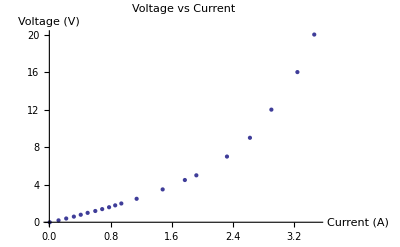

```mathematica
VvsI = Thread[{Current, V}]; 
ListPlot[{VvsI}, PlotLabel -> "Voltage vs Current", AxesLabel -> {"Current (A)", "Voltage (V)"}, PlotRange -> {{0.0,3.5}, {0.0,20.0}}]
```

As predicted in the introduction for Part 1, the relationship between Voltage and Current is non-linear in this case as its not ohmic. The Temperature clearly affects the values being recieved. As the temperature increases, voltages increases even more faster. Hence, the relationship between them at the very beginning is linear, however, as the temperature increases, the resistance changes and so does the voltage (the values start becoming exponential in a sense).

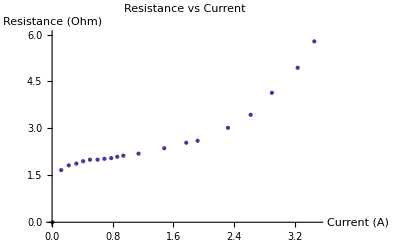

```mathematica
RvsI = Thread [{Current, R}];
ListPlot[{RvsI}, PlotLabel -> "Resistance vs Current", AxesLabel -> {"Current (A)", "Resistance (Ohm)"}, PlotRange -> {{0.0,3.5}, {0.0,6.0}}]
```

The plot shows that as current increases, the resistance increases in a much faster rate.

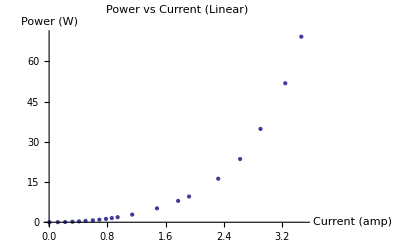

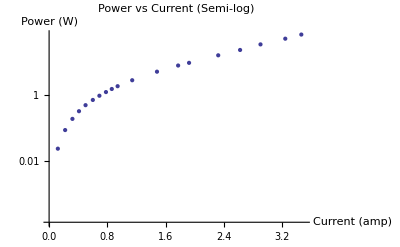

```mathematica
PvsI1 = Thread[{Current, P}];
ListPlot[{PvsI1}, PlotLabel -> "Power vs Current (Linear)", AxesLabel -> {"Current (amp)", "Power (W)"}, PlotRange -> {{0.0,3.5}, {0.0,70.0}}] (*Plots P vs I linearly*)
ListLogPlot[{PvsI1}, PlotLabel -> "Power vs Current (Semi-log)", AxesLabel -> {"Current (amp)", "Power (W)"}, PlotRange -> {{0.0,3.5}, {0.0,70.0}}]
```

Calculate the value R:
The calculated R when cold: 1.67 ± 0.01 Ohm
The calculated R when hot: 5.78 ± 0.01 Ohm
Maximum power: 69.20 ± 0.01 W
The measured value of R when cold: 1.20 ± 0.01 Ohm
The discrepency of R: [1.67-1.20] =0.47 ohm
The discrepency of 0.47 Ohm could be a result of not having an accurate instrument to measure the resistance. Internal resistance of the voltmeter and the wires could be a major factor into the discrepency. In order to not have this amount of discrepency, one should use wires with less internal resistance than the ones that were provided to us.

Part 2: Measurement of the frquency of a Periodic Signal

```mathematica
f = 1/T(*Equation to calculate Frequency (Hz)*)
δT = 1/1000.0 (*Error in the period measurement (s) in seconds*)
```

125

0.001

## Conclusion:

Part 1: IV Characteristic of Light Bulb

This part of the lab made us familiar with various instruments that were used to measure the current, voltage, and power. It helped us prove that the relationship between the current and voltage is non-linear when it comes to a non-omic resistance due to the fact that when it is ohmic resistor it has a constant resistance thus presenting a linear line, while the non-ohmic resistor it has more of an exponential line (non-linear). The concept behind this part is to show that as the filament current icnreases, the temperature increases. Increase in temperature then leads to the resistance increasing, resulting in a very non-linear IV characteristic.

Part 2: Measurement of the Frequency of a Periodic Signal

In conclusion, the calculations the measured frequency of the device was 125 Hz, almost double of the normal 60Hz value. This could be explained due to the diode (Measures power as P=V^2/R), concluding that the power has double the amount of frequency. When the photodiode was covered with our hands, majority of the light in the system was blocked leading to the fact that the measured amplitude was much lower than normal.